## Foreword, etc.

## Pre-amble

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
Needs["Combinatorica`"]
```

### Test

```mathematica
nCollatz[27]
```

{27,82,41,124,62,31,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1}

### Transfer to PKG

```mathematica
nDP[f_, g_] := Function[a, DivisorSum[a, f[#] g[a/#] &]]
```

```mathematica
nPrimesLEqThan[n_]:=Prime[Range[PrimePi[n]]]
nPrimesBetween[n_,m_]:=Module[
{a1,a2,rng},
If[n<=m,a1=m;a2=n,a1=n;a2=m];
rng=Complement[nPrimesLEqThan[a1],nPrimesLEqThan[a2]];
rng]
nPrimesBetween[100,150]
```

{101,103,107,109,113,127,131,137,139,149}

## Topic

### Definition / Theorem

This is text.

#### Example

## *Table of Arithmetical Functions ( -under construction- )

### Definition

#### Table

```mathematica
TableForm[{
{"Cell["I",ExpressionUUID->"77878252-9a1d-4b58-b066-202a47535308"]","-","Floor[1/n]","-","CM","I","?","1","1"},
{"1","-","1","-","CM","μ","?",DirichletTransform[1,n,s]//TraditionalForm,"1/(1-x)"},
{"N","-","n","-","CM","μN","?",DirichletTransform[n,n,s]//TraditionalForm,"1/(1-px)"},
{"N^a","a⩾0","n^a","σ_a*μ ; J_a*1","CM","μN^a","x^(a + 1)/(a+1)+O(x^a)",DirichletTransform[n^a,n,s]//TraditionalForm,"1/(1-p^ax)"},
{"μ","Sum of primitive\nn-th roots of unity","MoebiusMu[n]","-","M","1","?",DirichletTransform[MoebiusMu[n],n,s]//TraditionalForm,"1-x"},
{"μ_k","Möbius function of order k","nMoebiusMu[k,n]","-","M","?","?","?","?"},
{"ϕ","Euler Totient function","EulerPhi[n]","μ*N","M","μN*1","3/π^2 x^2 + O(x Log[x])",DirichletTransform[EulerPhi[n],n,s]//TraditionalForm,"(1-x)/(1-px)"},
{"J_k","Jordan Totient function","nJordanTotient[k,n]","μ*N^k ; σ_k*μ*μ","M","μN^k*1","?",DirichletTransform[DirichletConvolve[j^k,MoebiusMu[j],j,n],n,s]//TraditionalForm,"(p^k-1)/(1-p^kx)"},
{"τ","-","DivisorSigma[0,n]","1*1","M","μ*μ","x Log[x]+(2γ-1)x+O(√x)",DirichletTransform[DivisorSigma[0,n],n,s]//TraditionalForm,"1/(1-x)^2"},
{"τ^(k)","The number of ways of expressing n\nas a product of k positive factors","nDirichletPower\n[DivisorSigma[0,#]&,k][n]","1^(k + 1)","M","μ^(k + 1)","?","?","?"},
{"σ","-","DivisorSigma[1,n]","N*1 ; σ=ϕ*τ","M","μ*μN","ζ(2)/2 x^2+O(x Log[x])",DirichletTransform[DivisorSigma[1,n],n,s]//TraditionalForm,"1/((1-px)(1-x))"},
{"σ_a","a≥2","DivisorSigma[a,n]","N^a*1 ; σ_1=ϕ*τ","M","μ*μN^a","ζ(a+1)/(a+1)x^(a + 1)+O(x^a)","s-a s","1/((1-p^ax)(1-x))"},
{"GCD_k","-","GCD[k,n]","-","M","μGCD_k","?","?","?"},
{"γ","Core","-","-","M","?","?","?","(1-(1-p)x)/(1-x)"},
{"λ","-","LiouvilleLambda[n]\n(-1)^PrimeOmega[n]","-","M","μ^2 ; |μ|","?",DirichletTransform[LiouvilleLambda[n],n,s]//TraditionalForm,"1/(1+x)"},
{"μ^2","1 if squarefree, 0 otherwise","-","-","M","λ","?","ζ(s)/ζ(2s)","1+x"},
{"λ*1","1 if square, 0 otherwise","-","-","M","μ^2*μ","?","?","?"},
{"μ^2*1","Number of square-free divisors","2^PrimeNu[n]","|μ|*1","M","λ*μ","?",DirichletTransform[DirichletConvolve[1,Abs[MoebiusMu[j]],j,n],n,s]//TraditionalForm,"(1+x)/(1-x)"},
{"a","Number of abelian groups","FiniteAbelianGroupCount[n]","-","M","?","?","?","?"},
{"ϕ_k","Euler Totient function of order k","nEulerPhi[k,n]","Faulhaber_k*μN^k","-","?","?","?","?"},
{"ν","-","PrimeNu[n]","-","A","None","?","?","?"},
{"Ω","-","PrimeOmega[n]","-","CA","None","?","?","?"},
{"Λ","-","MangoldtLambda[n]","-","-","None","?","-ζ'(s)/ζ(s)","?"},
{"L","-","Log[n]","Λ*1","CA","None","?","?","?"},
{"ν*μ","1 if prime, 0 otherwise","-","-","?","None","?","?","?"},
{"?","1 if k-th-powerfree, 0 otherwise","-","-","?","?","?","ζ(s)/ζ(ks)","?"},
{"?","Von Sterneck function","-","-","?","?","?","?","?"},
{"?","Lehmer Divisor function","-","-","?","?","?","?","?"},
{"?","Ramanujan sum","-","-","?","?","?","?","?"},
{"M_k","Lehmer Inverse","-","-","M","?","?","?","?"},
{"S","Number of divisors of n^2","-","1*2^PrimeNu","M","?","?","?","?"}
},TableHeadings->{None,{"ARF","Remark", "Mathematica","Alt. Def.","(C)M/A/-","Inverse","Asymptotic ∑_(n ⩽ x) ", "Dirichlet Series", "Bell Series"}}]
```

ARF | Remark | Mathematica | Alt. Def. | (C)M/A/- | Inverse | Asymptotic ∑_(n ⩽ x)  | Dirichlet Series | Bell Series
Cell["I"] | - | Floor[1/n] | - | CM | I | ? | 1 | 1
1 | - | 1 | - | CM | μ | ? | s | 1/(1-x)
N | - | n | - | CM | μN | ? | s-1 | 1/(1-px)
N^a | a⩾0 | n^a | σ_a*μ ; J_a*1 | CM | μN^a | x^(a + 1)/(a+1)+O(x^a) | s-a | 1/(1-p^ax)
μ | Sum of primitive
n-th roots of unity | MoebiusMu[n] | - | M | 1 | ? | 1/s | 1-x
μ_k | Möbius function of order k | nMoebiusMu[k,n] | - | M | ? | ? | ? | ?
ϕ | Euler Totient function | EulerPhi[n] | μ*N | M | μN*1 | 3/π^2 x^2 + O(x Log[x]) | (s-1)/s | (1-x)/(1-px)
J_k | Jordan Totient function | nJordanTotient[k,n] | μ*N^k ; σ_k*μ*μ | M | μN^k*1 | ? | (s-k)/s | (p^k-1)/(1-p^kx)
τ | - | DivisorSigma[0,n] | 1*1 | M | μ*μ | x Log[x]+(2γ-1)x+O(√x) | s^2 | 1/(1-x)^2
τ^(k) | The number of ways of expressing n
as a product of k positive factors | nDirichletPower
[DivisorSigma[0,#]&,k][n] | 1^(k + 1) | M | μ^(k + 1) | ? | ? | ?
σ | - | DivisorSigma[1,n] | N*1 ; σ=ϕ*τ | M | μ*μN | ζ(2)/2 x^2+O(x Log[x]) | s-1 s | 1/((1-px)(1-x))
σ_a | a≥2 | DivisorSigma[a,n] | N^a*1 ; σ_1=ϕ*τ | M | μ*μN^a | ζ(a+1)/(a+1)x^(a + 1)+O(x^a) | s-a s | 1/((1-p^ax)(1-x))
GCD_k | - | GCD[k,n] | - | M | μGCD_k | ? | ? | ?
γ | Core | - | - | M | ? | ? | ? | (1-(1-p)x)/(1-x)
λ | - | LiouvilleLambda[n]
(-1)^PrimeOmega[n] | - | M | μ^2 ; |μ| | ? | (2 s)/s | 1/(1+x)
μ^2 | 1 if squarefree, 0 otherwise | - | - | M | λ | ? | ζ(s)/ζ(2s) | 1+x
λ*1 | 1 if square, 0 otherwise | - | - | M | μ^2*μ | ? | ? | ?
μ^2*1 | Number of square-free divisors | 2^PrimeNu[n] | |μ|*1 | M | λ*μ | ? | s^2/(2 s) | (1+x)/(1-x)
a | Number of abelian groups | FiniteAbelianGroupCount[n] | - | M | ? | ? | ? | ?
ϕ_k | Euler Totient function of order k | nEulerPhi[k,n] | Faulhaber_k*μN^k | - | ? | ? | ? | ?
ν | - | PrimeNu[n] | - | A | None | ? | ? | ?
Ω | - | PrimeOmega[n] | - | CA | None | ? | ? | ?
Λ | - | MangoldtLambda[n] | - | - | None | ? | -ζ'(s)/ζ(s) | ?
L | - | Log[n] | Λ*1 | CA | None | ? | ? | ?
ν*μ | 1 if prime, 0 otherwise | - | - | ? | None | ? | ? | ?
? | 1 if k-th-powerfree, 0 otherwise | - | - | ? | ? | ? | ζ(s)/ζ(ks) | ?
? | Von Sterneck function | - | - | ? | ? | ? | ? | ?
? | Lehmer Divisor function | - | - | ? | ? | ? | ? | ?
? | Ramanujan sum | - | - | ? | ? | ? | ? | ?
M_k | Lehmer Inverse | - | - | M | ? | ? | ? | ?
S | Number of divisors of n^2 | - | 1*2^PrimeNu | M | ? | ? | ? | ?

#### Example-1

So...: ∏_(d|n) (-1)^(Ω(d))(μ(n/d))^2=I(n)?

```mathematica
Table[{n,DirichletConvolve[Floor[1/k],DirichletConvolve[(-1)^PrimeOmega[j],Abs[MoebiusMu[j]],j,k],k,n]},{n,1,8}]//tf
DirichletTransform[DirichletConvolve[DivisorSigma[0,k],DirichletConvolve[1,Abs[MoebiusMu[j]],j,k],k,n],n,s]
```

1 | 1
2 | 0
3 | 0
4 | 0
5 | 0
6 | 0
7 | 0
8 | 0

Zeta[s]^4/Zeta[2 s]

```mathematica
Table[{k,2^PrimeNu[k]},{k,1,8}]//tf
```

1 | 1
2 | 2
3 | 2
4 | 2
5 | 2
6 | 4
7 | 2
8 | 2

## [ TBD: ] CONSTRUCTION OF THE INTEGERS

Notes:
a+d = b+c
(a+c, b+d)
(ac + bd, ad + bc )

## Bijection between ℕ and ℚ

### Experiments

```mathematica
Table[{k,nNaturalToQuotient[k]},{k,1,21}]//tf
```

1 | 0
2 | -1
3 | 1
4 | -1/2
5 | 1/2
6 | -1/3
7 | 1/3
8 | -2
9 | 2
10 | -1/5
11 | 1/5
12 | -1/6
13 | 1/6
14 | -1/7
15 | 1/7
16 | -1/4
17 | 1/4
18 | -3
19 | 3
20 | -1/10
21 | 1/10

```mathematica
nQuotientToNatural[5/2]
nQuotientToNatural[-1/53]
nQuotientToNatural[1/55]
```

101

106

111

```mathematica
Table[{k,nNaturalToQuotient[k]},{k,6606600,6606609}]
```

{{6606600,-110/273},{6606601,110/273},{6606602,-1/3303301},{6606603,1/3303301},{6606604,-1/3303302},{6606605,1/3303302},{6606606,-1/3303303},{6606607,1/3303303},{6606608,-1/1651652},{6606609,1/1651652}}

## tmp-1 ( Sum expression for Zeta(3) )

```mathematica
(-4 π^2)/7 Sum[Zeta[2k]/((2k+1)(2k+2)2^(2k)),{k,0,10}]//N
```

1.20206

```mathematica
Zeta[3]//N
```

1.20206

```mathematica
-4 π^2 Zeta'[-2]//N
```

1.20206

## nRandomLargePrimes

```mathematica
nDP[f_, g_] := Function[a, DivisorSum[a, f[#] g[a/#] &]]
```

```mathematica
Table[{k,nDP[2^PrimeNu[#]&,(-1)^PrimeOmega[#]&][k]},{k,1,12}]// tf
```

1 | 1
2 | 1
3 | 1
4 | 1
5 | 1
6 | 1
7 | 1
8 | 1
9 | 1
10 | 1
11 | 1
12 | 1

```mathematica
nRandomLargePrimes={
1493681662543217878160621001493954482728761115029,
700739825495796892911470158595612191109099877292529,
1472096224144293702191366558640187434517863879629549,
2103773991264901723662580595147397654330635569039357,
2699243374499511472600789225180130783824859693484071,
398869148505334498610415829456039133740158757895987873,
549335317644366848620963598863612623797226033046822367,
1404331202801782850289552174866956170276744436689685661,
3193363039935965772365112697679561879002491633999044243,
16584481766395224445084325459256163383388354525876508557,
141219010751766643014541882207227887046904103493608636851,
308287092487477895094790383880763507229711563200387863779,
1400142646836180704088519408419116252818995710960172965243,
215108727189576815121508725751291721300023431942578921304283,
2158853164829929621820714762594477555397898278329482309747283,
20803237077583935736984609616651585718892273678491880706401153,
170192827244567637928627699850632238942014026794841802229591029,
22712761749503233807399473845700967947686275009367417295274790267,
670560185136141781047307957731270637430080412253382216571221454743,
33700436725730370103570399037732371300367702399100433767036365707703
};
nRandomLargePrimes//Length
```

20

```mathematica
Table[Length[IntegerDigits[k]],{k,nRandomLargePrimes}]
```

{49,51,52,52,52,54,54,55,55,56,57,57,58,60,61,62,63,65,66,68}

```mathematica
FactorInteger[10110310710911312713100000002003000001151061067069071073079083089097]
```

{{251,1},{1069,1},{55373,1},{59107,1},{3204048763,1},{111856839257,1},{126892254017,1},{253150816870736542139,1}}

```mathematica
FactorInteger[4520189026299330782353421687996961553+10^70+144^15+13]
```

{{2,1},{3,1},{5,1},{7,1},{11251,1},{395741,1},{6369875290950186450136086793,1},{1678988045311068808536988947913,1}}

## Arithmetical Functions

## *Table of Arithmetical Functions ( -under construction- )

### Definition

#### Table

```mathematica
TableForm[{
{"Cell["I",ExpressionUUID->"77878252-9a1d-4b58-b066-202a47535308"]","-","Floor[1/n]","-","CM","I","?","1","1"},
{"1","-","1","-","CM","μ","?",DirichletTransform[1,n,s]//TraditionalForm,"1/(1-x)"},
{"N","-","n","-","CM","μN","?",DirichletTransform[n,n,s]//TraditionalForm,"1/(1-px)"},
{"N^a","a⩾0","n^a","σ_a*μ ; J_a*1","CM","μN^a","x^(a + 1)/(a+1)+O(x^a)",DirichletTransform[n^a,n,s]//TraditionalForm,"1/(1-p^ax)"},
{"μ","Sum of primitive\nn-th roots of unity","MoebiusMu[n]","-","M","1","?",DirichletTransform[MoebiusMu[n],n,s]//TraditionalForm,"1-x"},
{"μ_k","Möbius function of order k","nMoebiusMu[k,n]","-","M","?","?","?","?"},
{"ϕ","Euler Totient function","EulerPhi[n]","μ*N","M","μN*1","3/π^2 x^2 + O(x Log[x])",DirichletTransform[EulerPhi[n],n,s]//TraditionalForm,"(1-x)/(1-px)"},
{"J_k","Jordan Totient function","nJordanTotient[k,n]","μ*N^k ; σ_k*μ*μ","M","μN^k*1","?",DirichletTransform[DirichletConvolve[j^k,MoebiusMu[j],j,n],n,s]//TraditionalForm,"(p^k-1)/(1-p^kx)"},
{"τ","-","DivisorSigma[0,n]","1*1","M","μ*μ","x Log[x]+(2γ-1)x+O(√x)",DirichletTransform[DivisorSigma[0,n],n,s]//TraditionalForm,"1/(1-x)^2"},
{"τ^(k)","The number of ways of expressing n\nas a product of k positive factors","nDirichletPower\n[DivisorSigma[0,#]&,k][n]","1^(k + 1)","M","μ^(k + 1)","?","?","?"},
{"σ","-","DivisorSigma[1,n]","N*1 ; σ=ϕ*τ","M","μ*μN","ζ(2)/2 x^2+O(x Log[x])",DirichletTransform[DivisorSigma[1,n],n,s]//TraditionalForm,"1/((1-px)(1-x))"},
{"σ_a","a≥2","DivisorSigma[a,n]","N^a*1 ; σ_1=ϕ*τ","M","μ*μN^a","ζ(a+1)/(a+1)x^(a + 1)+O(x^a)","s-a s","1/((1-p^ax)(1-x))"},
{"GCD_k","-","GCD[k,n]","-","M","μGCD_k","?","?","?"},
{"γ","Core","-","-","M","?","?","?","(1-(1-p)x)/(1-x)"},
{"λ","-","LiouvilleLambda[n]\n(-1)^PrimeOmega[n]","-","M","μ^2 ; |μ|","?",DirichletTransform[LiouvilleLambda[n],n,s]//TraditionalForm,"1/(1+x)"},
{"μ^2","1 if squarefree, 0 otherwise","-","-","M","λ","?","ζ(s)/ζ(2s)","1+x"},
{"λ*1","1 if square, 0 otherwise","-","-","M","μ^2*μ","?","?","?"},
{"μ^2*1","Number of square-free divisors","2^PrimeNu[n]","|μ|*1","M","λ*μ","?",DirichletTransform[DirichletConvolve[1,Abs[MoebiusMu[j]],j,n],n,s]//TraditionalForm,"(1+x)/(1-x)"},
{"a","Number of abelian groups","FiniteAbelianGroupCount[n]","-","M","?","?","?","?"},
{"ϕ_k","Euler Totient function of order k","nEulerPhi[k,n]","Faulhaber_k*μN^k","-","?","?","?","?"},
{"ν","-","PrimeNu[n]","-","A","None","?","?","?"},
{"Ω","-","PrimeOmega[n]","-","CA","None","?","?","?"},
{"Λ","-","MangoldtLambda[n]","-","-","None","?","-ζ'(s)/ζ(s)","?"},
{"L","-","Log[n]","Λ*1","CA","None","?","?","?"},
{"ν*μ","1 if prime, 0 otherwise","-","-","?","None","?","?","?"},
{"?","1 if k-th-powerfree, 0 otherwise","-","-","?","?","?","ζ(s)/ζ(ks)","?"},
{"?","Von Sterneck function","-","-","?","?","?","?","?"},
{"?","Lehmer Divisor function","-","-","?","?","?","?","?"},
{"?","Ramanujan sum","-","-","?","?","?","?","?"},
{"M_k","Lehmer Inverse","-","-","M","?","?","?","?"},
{"S","Number of divisors of n^2","-","1*2^PrimeNu","M","?","?","?","?"}
},TableHeadings->{None,{"ARF","Remark", "Mathematica","Alt. Def.","(C)M/A/-","Inverse","Asymptotic ∑_(n ⩽ x) ", "Dirichlet Series", "Bell Series"}}]
```

ARF | Remark | Mathematica | Alt. Def. | (C)M/A/- | Inverse | Asymptotic ∑_(n ⩽ x)  | Dirichlet Series | Bell Series
Cell["I"] | - | Floor[1/n] | - | CM | I | ? | 1 | 1
1 | - | 1 | - | CM | μ | ? | s | 1/(1-x)
N | - | n | - | CM | μN | ? | s-1 | 1/(1-px)
N^a | a⩾0 | n^a | σ_a*μ ; J_a*1 | CM | μN^a | x^(a + 1)/(a+1)+O(x^a) | s-a | 1/(1-p^ax)
μ | Sum of primitive
n-th roots of unity | MoebiusMu[n] | - | M | 1 | ? | 1/s | 1-x
μ_k | Möbius function of order k | nMoebiusMu[k,n] | - | M | ? | ? | ? | ?
ϕ | Euler Totient function | EulerPhi[n] | μ*N | M | μN*1 | 3/π^2 x^2 + O(x Log[x]) | (s-1)/s | (1-x)/(1-px)
J_k | Jordan Totient function | nJordanTotient[k,n] | μ*N^k ; σ_k*μ*μ | M | μN^k*1 | ? | (s-k)/s | (p^k-1)/(1-p^kx)
τ | - | DivisorSigma[0,n] | 1*1 | M | μ*μ | x Log[x]+(2γ-1)x+O(√x) | s^2 | 1/(1-x)^2
τ^(k) | The number of ways of expressing n
as a product of k positive factors | nDirichletPower
[DivisorSigma[0,#]&,k][n] | 1^(k + 1) | M | μ^(k + 1) | ? | ? | ?
σ | - | DivisorSigma[1,n] | N*1 ; σ=ϕ*τ | M | μ*μN | ζ(2)/2 x^2+O(x Log[x]) | s-1 s | 1/((1-px)(1-x))
σ_a | a≥2 | DivisorSigma[a,n] | N^a*1 ; σ_1=ϕ*τ | M | μ*μN^a | ζ(a+1)/(a+1)x^(a + 1)+O(x^a) | s-a s | 1/((1-p^ax)(1-x))
GCD_k | - | GCD[k,n] | - | M | μGCD_k | ? | ? | ?
γ | Core | - | - | M | ? | ? | ? | (1-(1-p)x)/(1-x)
λ | - | LiouvilleLambda[n]
(-1)^PrimeOmega[n] | - | M | μ^2 ; |μ| | ? | (2 s)/s | 1/(1+x)
μ^2 | 1 if squarefree, 0 otherwise | - | - | M | λ | ? | ζ(s)/ζ(2s) | 1+x
λ*1 | 1 if square, 0 otherwise | - | - | M | μ^2*μ | ? | ? | ?
μ^2*1 | Number of square-free divisors | 2^PrimeNu[n] | |μ|*1 | M | λ*μ | ? | s^2/(2 s) | (1+x)/(1-x)
a | Number of abelian groups | FiniteAbelianGroupCount[n] | - | M | ? | ? | ? | ?
ϕ_k | Euler Totient function of order k | nEulerPhi[k,n] | Faulhaber_k*μN^k | - | ? | ? | ? | ?
ν | - | PrimeNu[n] | - | A | None | ? | ? | ?
Ω | - | PrimeOmega[n] | - | CA | None | ? | ? | ?
Λ | - | MangoldtLambda[n] | - | - | None | ? | -ζ'(s)/ζ(s) | ?
L | - | Log[n] | Λ*1 | CA | None | ? | ? | ?
ν*μ | 1 if prime, 0 otherwise | - | - | ? | None | ? | ? | ?
? | 1 if k-th-powerfree, 0 otherwise | - | - | ? | ? | ? | ζ(s)/ζ(ks) | ?
? | Von Sterneck function | - | - | ? | ? | ? | ? | ?
? | Lehmer Divisor function | - | - | ? | ? | ? | ? | ?
? | Ramanujan sum | - | - | ? | ? | ? | ? | ?
M_k | Lehmer Inverse | - | - | M | ? | ? | ? | ?
S | Number of divisors of n^2 | - | 1*2^PrimeNu | M | ? | ? | ? | ?

#### Example-1

So...: ∏_(d|n) (-1)^(Ω(d))(μ(n/d))^2=I(n)?

```mathematica
Table[{n,DirichletConvolve[Floor[1/k],DirichletConvolve[(-1)^PrimeOmega[j],Abs[MoebiusMu[j]],j,k],k,n]},{n,1,8}]//tf
DirichletTransform[DirichletConvolve[DivisorSigma[0,k],DirichletConvolve[1,Abs[MoebiusMu[j]],j,k],k,n],n,s]
```

1 | 1
2 | 0
3 | 0
4 | 0
5 | 0
6 | 0
7 | 0
8 | 0

Zeta[s]^4/Zeta[2 s]

```mathematica
Table[{k,2^PrimeNu[k]},{k,1,8}]//tf
```

1 | 1
2 | 2
3 | 2
4 | 2
5 | 2
6 | 4
7 | 2
8 | 2

```mathematica
2^6 3^6 5^1  7^1 11^1
Divisors[2^6 3^6 5^1  7^1 11^1]//Length
```

17962560

392

```mathematica
2^11 3^7 5^5  7^3 11^2
12 8 6 4 3
Divisors[2^11 3^7 5^5  7^3 11^2]//Length
```

580909190400000

6912

6912

```mathematica
2^13 3^11 5^7  7^5 11^3 13^2
14 12 8 6 4 3
Divisors[2^13 3^11 5^7  7^5 11^3 13^2]//Length
```

428616352408083840000000

96768

96768

```mathematica
96768/6912
```

14

```mathematica
l1:=Primes[2]
l2:={2,3,4}
target:={2^2,4^3,6^4}
```

## DirichletConvolve, DirichletTransform

```mathematica
2 Log[2]/Log[12]+Log[3]/Log[12]//N
```

1.

```mathematica
Log[2]/Log[30]+Log[3]/Log[30]+Log[5]/Log[30]//N
```

1.

```mathematica
f[k_]:=DirichletConvolve[1,EulerPhi[n],n,k]
Table[{k,f[k]},{k,1,10}]//tf
```

1 | 1
2 | 2
3 | 3
4 | 4
5 | 5
6 | 6
7 | 7
8 | 8
9 | 9
10 | 10

```mathematica
f[k_]:=DirichletConvolve[1,MangoldtLambda[n],n,k]
f[k_]:=DirichletConvolve[1,MoebiusMu[n],n,k]
f[k_]:=DivisorSum[k,MoebiusMu[#]&]
Table[{k,-DivisorSum[k,MoebiusMu[#]Log[#]&]//Simplify,f[k]//Simplify},{k,1,10}]//tf;
Table[{k,f[k]},{k,1,10}]//tf
```

1 | 1
2 | 0
3 | 0
4 | 0
5 | 0
6 | 0
7 | 0
8 | 0
9 | 0
10 | 0

```mathematica
DirichletTransform[LiouvilleLambda[n],n,s]
DirichletTransform[MangoldtLambda[n],n,s]
```

Zeta[2 s]/Zeta[s]

-Zeta'[s]/Zeta[s]

## Ontbinding f[n_]:=1

```mathematica
f[n_]:=1
Table[{n,f[n]},{n,1,10}]//tf
```

1 | 1
2 | 1
3 | 1
4 | 1
5 | 1
6 | 1
7 | 1
8 | 1
9 | 1
10 | 1

```mathematica
g[n_]:=nDP[2^PrimeNu[#]&,(-1)^PrimeOmega[#]&][n]
Table[{n,g[n]},{n,1,10}]//tf
```

1 | 1
2 | 1
3 | 1
4 | 1
5 | 1
6 | 1
7 | 1
8 | 1
9 | 1
10 | 1

## Bakjes R&D

## Study Bellman

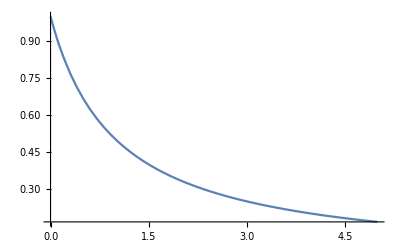

```mathematica
f[x_]:=1/(x+1)
Plot[f[x],{x,0,5}]
```

```mathematica
{Sum[f[k],{k,1,5}],Integrate[f[s],{s,0,5}],Sum[f[k],{k,0,4}]}//N
```

{1.45,1.79176,2.28333}

```mathematica
g[n_]:=Module[{v},If[n==2,
v="A",
If[n==3,
v="B",
v="Neither"
];
];
v
]/;IntegerQ[n]
```

## (* ERROR: - Enumerator for p q r - Dev - BUG *)

```mathematica
enumpq[n_]:=Module[{k=0,lst={}},
For[i=1,i<=n,i++,
For[j=1,j<i,j++,
k++;
lst=Append[lst,Prime[i]*Prime[j]];
];
];
lst
];
```

```mathematica
Select[enumpq[15],#<=100&]
```

{6,10,15,14,21,35,22,33,55,77,26,39,65,91,34,51,85,38,57,95,46,69,58,87,62,93,74,82,86,94}

```mathematica
enumpqr[n_]:=Module[{k=0,lst={}},
For[i=3,i<=n,i++,
For[j=1,j<=Prime[i],j++,
If[Mod[enumpq[[j]],Prime[i]]==0,Break[]];
k++;
Print[{k,l11[[j]]Prime[i]}];
];
]
]
```

## Bakjes-Info-[TBD]

```mathematica
viaPrt[n_]:=Flatten[Map[IntegerPartitions[#]&,Range[n]],1]
viaNum[n_]:=Module[{ls},
lst={};
For[i=2,i<n,i++,
lst=Append[lst,FactorInteger[i][[All,2]]]
];
Sort[DeleteDuplicates[DeleteDuplicates[lst,Sort[#1]==Sort[#2]&]]]
]

viaNum2[n_]:=Module[{ls},
lst={{0}};
For[i=2,i<(n+1),i++,
lst=Append[lst,Reverse[Sort[FactorInteger[i][[All,2]]]]]
];
lst
]

viaNum3[n_]:=Module[{ls},
lst={{0 ,{0}}};
For[i=2,i<(n+1),i++,
	lst=Append[lst,{Reverse[Sort[FactorInteger[i][[All,2]]]]}
]
];
lst
]
```

## Experiments: container (“Bakjes”) size

### Code to Transfer to Number Theory Package

```mathematica
nGetPrimeSignature[n_]:=Sort[FactorInteger[n][[All,2]]]

nBuildPrimeSignatureContainers[n_]:=Module[{assoc},
assoc=<|{0}->{1}|>;
If[
MissingQ[Lookup[assoc,{nGetPrimeSignature[#]}][[1]]],
assoc=AssociateTo[assoc,nGetPrimeSignature[#]->{#}],
assoc=AssociateTo[assoc,nGetPrimeSignature[#]->Append[Key[nGetPrimeSignature[#]][assoc],#]] 
]&/@Range[2,n];
assoc
]
```

### Alpha Tests

```mathematica
ds=nBuildPrimeSignatureContainers[100]//Dataset;
Normal[Values[KeySelect[ds,#=={1,1,1}&]]][[1]]//FactorInteger
```

{{{2,1},{3,1},{5,1}},{{2,1},{3,1},{7,1}},{{2,1},{3,1},{11,1}},{{2,1},{5,1},{7,1}},{{2,1},{3,1},{13,1}}}

### Building Subtrees

```mathematica
Prime[Range[PrimePi[10]]]
Normal[Values[KeySelect[ds,#=={1,1}&]]]
```

{2,3,5,7}

{{6,10,14,15,21,22,26,33,34,35,38,39,46,51,55,57,58,62,65,69,74,77,82,85,86,87,91,93,94,95}}

```mathematica
ls=(KeySelect[ds,#=={1,1}&]//Values//Normal)[[1]]

ls2=Select[ls,Not[Divisible[#,2]]&];
Complement[ls,ls2]

ls3=Select[ls2,Not[Divisible[#,3]]&];
Complement[ls2,ls3]

ls5=Select[ls3,Not[Divisible[#,5]]&];
Complement[ls3,ls5]

ls7=Select[ls5,Not[Divisible[#,7]]&];
Complement[ls5,ls7]

Union[ls,ls2,ls3,ls5,ls7]
FactorInteger[Union[ls,ls2,ls3,ls5,ls7]]
```

{6,10,14,15,21,22,26,33,34,35,38,39,46,51,55,57,58,62,65,69,74,77,82,85,86,87,91,93,94,95}

{6,10,14,22,26,34,38,46,58,62,74,82,86,94}

{15,21,33,39,51,57,69,87,93}

{35,55,65,85,95}

{77,91}

{6,10,14,15,21,22,26,33,34,35,38,39,46,51,55,57,58,62,65,69,74,77,82,85,86,87,91,93,94,95}

{{{2,1},{3,1}},{{2,1},{5,1}},{{2,1},{7,1}},{{3,1},{5,1}},{{3,1},{7,1}},{{2,1},{11,1}},{{2,1},{13,1}},{{3,1},{11,1}},{{2,1},{17,1}},{{5,1},{7,1}},{{2,1},{19,1}},{{3,1},{13,1}},{{2,1},{23,1}},{{3,1},{17,1}},{{5,1},{11,1}},{{3,1},{19,1}},{{2,1},{29,1}},{{2,1},{31,1}},{{5,1},{13,1}},{{3,1},{23,1}},{{2,1},{37,1}},{{7,1},{11,1}},{{2,1},{41,1}},{{5,1},{17,1}},{{2,1},{43,1}},{{3,1},{29,1}},{{7,1},{13,1}},{{3,1},{31,1}},{{2,1},{47,1}},{{5,1},{19,1}}}

## Bakjes R&D Devs

## Prototype-1 ( Without prsig={1,1} )

```mathematica
nGetPrimeSignature[n_]:=Sort[FactorInteger[n][[All,2]]]

nBuildPrimeSignatureContainers[n_]:=Module[{assoc,k,prsig,m},

assoc=<|{0}->{1}|>;
For[k=2,k<=n,k++,
prsig=nGetPrimeSignature[k];
If[
MissingQ[Lookup[assoc,{prsig}][[1]]],
AssociateTo[assoc,prsig->{k}],
assoc=AssociateTo[assoc,prsig->Append[Key[prsig][assoc],k]] ;
];
];
assoc
]                                                                                                                                                                                                                                              

nBuildPrimeSignatureContainers[31]
```

<|{0}→{1},{1}→{2,3,5,7,11,13,17,19,23,29,31},{2}→{4,9,25},{1,1}→{6,10,14,15,21,22,26},{3}→{8,27},{1,2}→{12,18,20,28},{4}→{16},{1,3}→{24},{1,1,1}→{30}|>

## Prototype-2: ( Without prsig = {1,1,1, ...} ) /* Code likely NOT optimal / efficient */

```mathematica
nGetPrimeSignature[n_]:=Sort[FactorInteger[n][[All,2]]]

nBuildPrimeSignatureContainers[n_]:=Module[{assoc,k,prsig,m},
assoc=<|{0}->{1}|>;

For[k=2,k<=n,k++,
prsig=nGetPrimeSignature[k];
m=Sort[FactorInteger[k][[All,1]]][[1]];
If[prsig=={1,1},
If[MissingQ[assoc[[Key[prsig]]]],
assoc=Association[assoc,prsig-><|{m,"p"}->{k}|>];,
If[MissingQ[assoc[prsig][{m,"p"}]],
assoc[prsig]=Association[Key[prsig][assoc],{m,"p"}->{k}],
AppendTo[assoc[prsig][{m,"p"}],k];
];
];,
If[MissingQ[assoc[[Key[prsig]]]],
assoc=Association[assoc,prsig->{k}],
AppendTo[assoc[[Key[prsig]]],k]];
];
];
assoc
]
```

### Demonstrations / Test-runs

```mathematica
data=Timing[nBuildPrimeSignatureContainers[18]]
```

{0.,<|{0}→{1},{1}→{2,3,5,7,11,13,17},{2}→{4,9},{1,1}→<|{2,p}→{6,10,14},{3,p}→{15}|>,{3}→{8},{1,2}→{12,18},{4}→{16}|>}

```mathematica
data//Dataset
```

### Other subject---

```mathematica
Table[StirlingS2[n,k],{n,0,12},{k,0,n}]//tf
```

1 |  |  |  |  |  |  |  |  |  |  |  | 
0 | 1 |  |  |  |  |  |  |  |  |  |  | 
0 | 1 | 1 |  |  |  |  |  |  |  |  |  | 
0 | 1 | 3 | 1 |  |  |  |  |  |  |  |  | 
0 | 1 | 7 | 6 | 1 |  |  |  |  |  |  |  | 
0 | 1 | 15 | 25 | 10 | 1 |  |  |  |  |  |  | 
0 | 1 | 31 | 90 | 65 | 15 | 1 |  |  |  |  |  | 
0 | 1 | 63 | 301 | 350 | 140 | 21 | 1 |  |  |  |  | 
0 | 1 | 127 | 966 | 1701 | 1050 | 266 | 28 | 1 |  |  |  | 
0 | 1 | 255 | 3025 | 7770 | 6951 | 2646 | 462 | 36 | 1 |  |  | 
0 | 1 | 511 | 9330 | 34105 | 42525 | 22827 | 5880 | 750 | 45 | 1 |  | 
0 | 1 | 1023 | 28501 | 145750 | 246730 | 179487 | 63987 | 11880 | 1155 | 55 | 1 | 
0 | 1 | 2047 | 86526 | 611501 | 1379400 | 1323652 | 627396 | 159027 | 22275 | 1705 | 66 | 1

```mathematica
IntegerName[1000000,{"Dutch"}]
IntegerName[1000000000,{"Dutch"}]
IntegerName[1000000000000,{"Dutch"}]
IntegerName[1000000000000000,{"Dutch"}]

IntegerName[1000000]
IntegerName[1000000000]
IntegerName[1000000000000]
IntegerName[1000000000000000]
```

een miljoen

een miljard

een biljoen

een biljard

1 million

1 billion

1 trillion

1 quadrillion

```mathematica
X={a,b,c}
```

{a,b,c}

```mathematica
nGetPrimeSignature[100]
```

{2,2}

```mathematica
FactorInteger[100]
```

{{2,2},{5,2}}

```mathematica
Y={2,2,5,5};
DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]
```

{{{2,2,5,5}},{{2},{2,5,5}},{{2,2},{5,5}},{{5},{2,2,5}},{{2,5},{2,5}},{{2},{2},{5,5}},{{2},{5},{2,5}},{{5},{5},{2,2}},{{2},{2},{5},{5}}}

```mathematica
Array[2&,2]
```

{2,2}

```mathematica
ClearAll[f]
f[{x_,y_}]:=Array[x&,y]
f[{2,3}]
f[{3,2}]
```

{2,2,2}

{3,3}

```mathematica
Y=Flatten[Append[Append[f[{2,3}],f[{3,1}]],f[{5,1}]]]
DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]//Length
```

{2,2,2,3,5}

21

```mathematica
Join[{1},{3,3,4},{5}]
```

{1,3,3,4,5}

```mathematica
Y=Map[f[{#[[1]],#[[2]]}]&,FactorInteger[96]]//Flatten
DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]//Length
Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]]
```

{f[{2,5}],f[{3,1}]}

2

{{{f[{2,5}],f[{3,1}]}},{{f[{2,5}]},{f[{3,1}]}}}

```mathematica
lst={
{{2,2,2,2,2,3}},
{{2},{2,2,2,2,3}},
{{2,2},{2,2,2,3}},
{{2,2,2},{2,2,3}},
{{2,3},{2,2,2,2}},
{{3},{2,2,2,2,2}},
{{2},{2},{2,2,2,3}},
{{2},{2,2},{2,2,3}},
{{2},{2,3},{2,2,2}},
{{2},{3},{2,2,2,2}},
{{2,2},{2,2},{2,3}},
{{3},{2,2},{2,2,2}},{{2},{2},{2},{2,2,3}},{{2},{2},{2,2},{2,3}},{{2},{2},{3},{2,2,2}},{{2},{3},{2,2},{2,2}},{{2},{2},{2},{2},{2,3}},{{2},{2},{2},{3},{2,2}},{{2},{2},{2},{2},{2},{3}}};
```

```mathematica
Map[Apply[Times,#]&,lst,{2}]//tf
```

96 |  |  |  |  | 
2 | 48 |  |  |  | 
4 | 24 |  |  |  | 
8 | 12 |  |  |  | 
6 | 16 |  |  |  | 
3 | 32 |  |  |  | 
2 | 2 | 24 |  |  | 
2 | 4 | 12 |  |  | 
2 | 6 | 8 |  |  | 
2 | 3 | 16 |  |  | 
4 | 4 | 6 |  |  | 
3 | 4 | 8 |  |  | 
2 | 2 | 2 | 12 |  | 
2 | 2 | 4 | 6 |  | 
2 | 2 | 3 | 8 |  | 
2 | 3 | 4 | 4 |  | 
2 | 2 | 2 | 2 | 6 | 
2 | 2 | 2 | 3 | 4 | 
2 | 2 | 2 | 2 | 2 | 3

```mathematica
Apply[Times,{2,3,4}]
```

24

```mathematica
FactorInteger[420]
```

{{2,2},{3,1},{5,1},{7,1}}

```mathematica
(* iets met Function *)
ClearAll[f]
f[{x_,y_}]:=Array[x&,y]
Y=Map[f[{#[[1]],#[[2]]}]&,FactorInteger[2 2 3 3]]//Flatten
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]//Length
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]//tf
```

{2,2,3,3}

9

{{36},{2,18},{4,9},{3,12},{6,6},{2,2,9},{2,3,6},{3,3,4},{2,2,3,3}}

36 |  |  | 
2 | 18 |  | 
4 | 9 |  | 
3 | 12 |  | 
6 | 6 |  | 
2 | 2 | 9 | 
2 | 3 | 6 | 
3 | 3 | 4 | 
2 | 2 | 3 | 3

```mathematica
ClearAll[f]
f[{x_,y_}]:=Array[x&,y]
Y=Map[f[{#[[1]],#[[2]]}]&,FactorInteger[2 2 2 3 3]]//Flatten
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]//Length
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]//tf
```

{2,2,2,3,3}

16

{{72},{2,36},{4,18},{9,8},{3,24},{6,12},{2,2,18},{2,4,9},{2,3,12},{2,6,6},{3,4,6},{3,3,8},{2,2,2,9},{2,2,3,6},{2,3,3,4},{2,2,2,3,3}}

72 |  |  |  | 
2 | 36 |  |  | 
4 | 18 |  |  | 
9 | 8 |  |  | 
3 | 24 |  |  | 
6 | 12 |  |  | 
2 | 2 | 18 |  | 
2 | 4 | 9 |  | 
2 | 3 | 12 |  | 
2 | 6 | 6 |  | 
3 | 4 | 6 |  | 
3 | 3 | 8 |  | 
2 | 2 | 2 | 9 | 
2 | 2 | 3 | 6 | 
2 | 3 | 3 | 4 | 
2 | 2 | 2 | 3 | 3

```mathematica
Y=Map[f[{#[[1]],#[[2]]}]&,FactorInteger[2 3 3 ]]//Flatten
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]
```

{2,3,3}

{{18},{2,9},{3,6},{2,3,3}}

```mathematica
Y=Map[f[{#[[1]],#[[2]]}]&,FactorInteger[6]]//Flatten
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]
```

{2,3}

{{6},{2,3}}

```mathematica
Y=Map[f[{#[[1]],#[[2]]}]&,FactorInteger[12]]//Flatten
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]
```

{2,2,3}

{{12},{2,6},{3,4},{2,2,3}}

### tmp

```mathematica
ClearAll[f]
f[{x_,y_}]:=Array[x&,y]
Y=Map[f[{#[[1]],#[[2]]}]&,FactorInteger[2 2 3 3]]//Flatten
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]//Length
```

```mathematica
ClearAll[f]
f[{x_,y_}]:=Array[x&,y]
Y=Map[f[{#[[1]],#[[2]]}]&,FactorInteger[2 2 3 3]]//Flatten
Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Y]]]],{2}]//Length
```

```mathematica
Flatten[Map[Function[x,Array[x[[1]]&,x [[2]]]],FactorInteger[72]]]
```

{{2,2,2},{3,3}}

```mathematica
nFactorListInteger[n_]:=Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Flatten[Map[Function[x,Array[x[[1]]&,x [[2]]]],FactorInteger[n]]]]]]],{2}]
```

```mathematica
lst=nFactorListInteger[10000]//Length
```

109

```mathematica
Table[StirlingS2[n,k],{n,0,6},{k,0,n}]//tf
```

1 |  |  |  |  |  | 
0 | 1 |  |  |  |  | 
0 | 1 | 1 |  |  |  | 
0 | 1 | 3 | 1 |  |  | 
0 | 1 | 7 | 6 | 1 |  | 
0 | 1 | 15 | 25 | 10 | 1 | 
0 | 1 | 31 | 90 | 65 | 15 | 1

```mathematica
PartitionsP[4]
```

5

```mathematica
BellB[4]
```

15

```mathematica
117 17
```

1989

```mathematica
nFactorListInteger[30]//tf
```

30 |  | 
2 | 15 | 
5 | 6 | 
3 | 10 | 
2 | 3 | 5

```mathematica
Solve[2^x (2y+1)==z&& x>0&&y>0&&z>0&&x==3&&z>0&&z<=48,{y,z},Integers]
```

{{y→ConditionalExpression[1, x==3],z→ConditionalExpression[24, x==3]},{y→ConditionalExpression[2, x==3],z→ConditionalExpression[40, x==3]}}

## Prepare nFactorListInteger => Number Theory Package

```mathematica
nFactorListIntegerDEV[n_]:=Map[Apply[Times,#]&,Map[#&,DeleteDuplicates[Map[Sort[#]&,SetPartitions[Flatten[Map[Function[x,Array[x[[1]]&,x [[2]]]],FactorInteger[n]]]]]]],{2}]
```